```mathematica
Integrate[(Abs[Δ]^2/(Abs[Δ]^2-ϵ^2))*(Abs[δ]/(Abs[δ]^2+ϵ^2))*(2-ϵ^2/(Abs[Δ]^2-ϵ^2)),{ϵ,-Abs[n*δ],Abs[n*δ]}]
```

ConditionalExpression[(Abs[Δ] (8 Δ^2 (Δ^2-Abs[n δ]^2) Abs[Δ] ArcTan[Abs[n δ]/Abs[δ]]+12 Abs[δ]^2 (Δ^2-Abs[n δ]^2) Abs[Δ] ArcTan[Abs[n δ]/Abs[δ]]+Δ^2 Abs[δ] (-2 Abs[n δ] Abs[Δ]+3 ⅈ Δ^2 (π+ⅈ Log[(Abs[n δ]-Abs[Δ])/(Abs[n δ]+Abs[Δ])])+3 Abs[n δ]^2 (-ⅈ π+Log[Abs[n δ]-Abs[Δ]]-Log[Abs[n δ]+Abs[Δ]]))+Abs[δ]^3 (-2 Abs[n δ] Abs[Δ]+5 ⅈ Δ^2 (π+ⅈ Log[(Abs[n δ]-Abs[Δ])/(Abs[n δ]+Abs[Δ])])+5 Abs[n δ]^2 (-ⅈ π+Log[Abs[n δ]-Abs[Δ]]-Log[Abs[n δ]+Abs[Δ]]))))/(2 (Δ^2+Abs[δ]^2)^2 (Δ^2-Abs[n δ]^2)),Δ∈Reals&&(Im[n]≠0||Re[n]≠0)&&(Im[δ]≠0||Re[δ]≠0)]

```mathematica
(Δ^2/(Δ^2-ϵ^2))*(δ/(δ^2+ϵ^2))*(2-ϵ^2/(Δ^2-ϵ^2))
```

(δ Δ^2 (2-ϵ^2/(Δ^2-ϵ^2)))/((Δ^2-ϵ^2) (δ^2+ϵ^2))

```mathematica
F[δ_,Δ_,n_]:=(Abs[Δ] (8 Δ^2 (Δ^2-Abs[n δ]^2) Abs[Δ] ArcTan[Abs[n δ]/Abs[δ]]+12 Abs[δ]^2 (Δ^2-Abs[n δ]^2) Abs[Δ] ArcTan[Abs[n δ]/Abs[δ]]+Δ^2 Abs[δ] (-2 Abs[n δ] Abs[Δ]+3 ⅈ Δ^2 (π+ⅈ Log[(Abs[n δ]-Abs[Δ])/(Abs[n δ]+Abs[Δ])])+3 Abs[n δ]^2 (-ⅈ π+Log[Abs[n δ]-Abs[Δ]]-Log[Abs[n δ]+Abs[Δ]]))+Abs[δ]^3 (-2 Abs[n δ] Abs[Δ]+5 ⅈ Δ^2 (π+ⅈ Log[(Abs[n δ]-Abs[Δ])/(Abs[n δ]+Abs[Δ])])+5 Abs[n δ]^2 (-ⅈ π+Log[Abs[n δ]-Abs[Δ]]-Log[Abs[n δ]+Abs[Δ]]))))/(2 (Δ^2+Abs[δ]^2)^2 (Δ^2-Abs[n δ]^2));
FullSimplify[Re[F[Abs[δ],Abs[Δ],n]]]
```

(-2 Δ Abs[n δ^4 Δ]-2 Δ Abs[n δ^2 Δ^3]+4 Δ Abs[Δ] ArcTan[Abs[n]] (Abs[Δ]^2-n δ Conjugate[n] Conjugate[δ]) (3 δ Conjugate[δ]+2 Δ Conjugate[Δ])+Δ Abs[δ] (5 δ Conjugate[δ]+3 Δ Conjugate[Δ]) Re[Abs[n δ]^2 Log[Abs[n δ]-Abs[Δ]]-Abs[Δ]^2 Log[-1+(2 Abs[n] Abs[δ])/(Abs[n δ]+Abs[Δ])]]-Abs[n^2 δ^3 Δ] (5 δ Conjugate[δ]+3 Δ Conjugate[Δ]) Re[Log[Abs[n δ]+Abs[Δ]]] Sign[Δ])/(2 (Abs[δ]^2+Abs[Δ]^2)^2 (Abs[Δ]^2-n δ Conjugate[n] Conjugate[δ]) Sign[Δ])

6.06971-2.77556×10^-17 Re[Log[Abs[Δ]]]

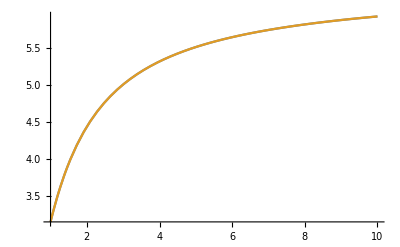

```mathematica
F2[δ_,Δ_,n_] = (-2 Δ Abs[n δ^4 Δ]-2 Δ Abs[n δ^2 Δ^3]+4 Δ Abs[Δ] ArcTan[Abs[n]] (Abs[Δ]^2-n δ Conjugate[n] Conjugate[δ]) (3 δ Conjugate[δ]+2 Δ Conjugate[Δ])+Δ Abs[δ] (5 δ Conjugate[δ]+3 Δ Conjugate[Δ]) Re[Abs[n δ]^2 Log[Abs[n δ]-Abs[Δ]]-Abs[Δ]^2 Log[-1+(2 Abs[n] Abs[δ])/(Abs[n δ]+Abs[Δ])]]-Abs[n^2 δ^3 Δ] (5 δ Conjugate[δ]+3 Δ Conjugate[Δ]) Re[Log[Abs[n δ]+Abs[Δ]]] Sign[Δ])/(2 (Abs[δ]^2+Abs[Δ]^2)^2 (Abs[Δ]^2-n δ Conjugate[n] Conjugate[δ]) Sign[Δ]);
FullSimplify[F2[0.05Abs[Δ],Abs[Δ],15]]
Plot[{F2[0.05Abs[1],Abs[1],n],F2[0.05Abs[2],Abs[2],n]},{n,1,10}]
```